# Kotashevich_S_N Lab_work_5: Введение в

## Задание 1

### а) Пробел выполняет роль знака умножения

```mathematica
3 5
```

15

### б) Введение дополнительных пробелов не изменяет результата вычислений

```mathematica
3           5
```

15

```mathematica
2 +       7
```

9

### в) Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя

```mathematica
2 / 3
```

2/3

```mathematica
17 ^ (1/2)
```

√17

### г) Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды

```mathematica
3 / 7.
```

0.428571

```mathematica
17. ^ (1/2)
```

4.12311

### д) Для изменения стандартного порядка выполнения операций используются круглые скобки

```mathematica
3 (2 + 5)
```

21

## Задание 2

### а) С помощью функции N вычислите √17 с точностью до 200 значащих цифр. Проверьте точность полученного результата с помощью функции Precision

```mathematica
N[Sqrt[17], 200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
```

200.

### б) Найти приближенное значение числа ⅇ^(π √163) с точностью до 40 значащих цифр. Вычислите, на сколько полученный результат отличается от ближайшего к нему целого числа. Для стандартного округления чисел в системе Mathematica используется функция Round[x]

```mathematica
N[E^(Pi Sqrt[163]), 40]
```

2.625374126407687439999999999992500725972×10^17

```mathematica
Round[%]
```

262537412640768744

```mathematica
% - %%
```

7.499274028×10^-13

### в) Вычислите(10 * ((10.8 * 10^3)/300)^(1/2) + 4)^(1/3); (10^-24 * 10^12)/10^-14 √(32768/2^9)

```mathematica
(10 * ((10.8 * 10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 * 10^12)/10^-14 √(32768/2^9)
```

800

### г) Последовательно введите выражения 5 > 3 5 < 2 и посмотрите, что выдает Mathematica при их обработке. Затем определите, справедливо или нет неравенство π^ⅇ > ⅇ^π. Найдите численные значения левой и правой частей неравенства в правильности полученного результата

```mathematica
5 > 3
```

True

```mathematica
5≤ 3
```

False

```mathematica
Pi^E > E^Pi
```

False

```mathematica
N[Pi^E]
```

22.4592

```mathematica
N[E^Pi]
```

23.1407

## Задание 3

### а) Решить уравнения √(x + 2) + 4 x == 4; x^3 - 3 x^2 + 5 == 0

```mathematica
NSolve[√(x + 2) + 4 x == 4, x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3 - 3 x^2 + 5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

### б) Решить системы уравнений

```mathematica
NSolve[{x^2 + x y + y^2 == 1, x^3 + x^2 y + x y^2 + y^3 == 4}, {x, y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x - y^2 + 3 z == 34, x + y - z == -1, -x + 2 y + 3 z == 4}, {x, y, z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

### в) Придумайте уравнение или систему полиномиальных уравнений и найдите ее численное решение

```mathematica
NSolve[x^5 -2 x + 1 == 0, x]
```

{{x→-1.29065},{x→-0.114071-1.21675 ⅈ},{x→-0.114071+1.21675 ⅈ},{x→0.51879},{x→1.}}

## Задание 4

### 13. ch x - 2 = sin(x) на отрезке x ∈ [-1, 2]

```mathematica
FindRoot[Cosh[x] - 2 == Sin[x], {x, -1, 2}]
```

{x→-0.765191}

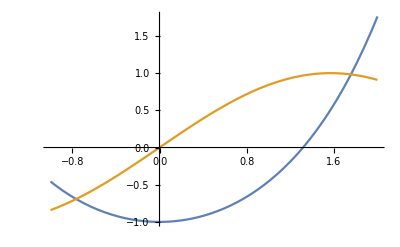

```mathematica
Plot[{Cosh[x] - 2, Sin[x]}, {x, -1, 2}]
```

## Задание 5

### 13. y’’ - 2y’ + 3 xy^3

```mathematica
sol1 = NDSolve[{y''[x] - 2 y'[x] + 3 x y[x]^3 == 0, y[0] == 0, y'[0] == 1}, y, {x, 0, 2} ]
```

{{y→InterpolatingFunction[…]}}

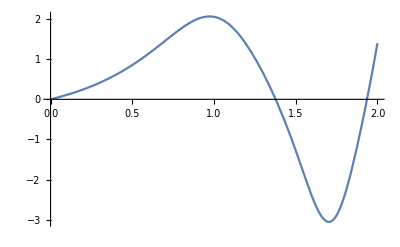

```mathematica
Plot[y[x] /. sol1, {x, 0, 2}]
```

### а) найдите на заданном отрезке корни уравнения у(х) = 0

```mathematica
sol2 = FindRoot[(y[x] /. sol1[[1]]) == 0, {x, 1.38}]
```

{x→1.37709}

### б) найдите значение производной y’(x) в точках, где у(х) = 0

```mathematica
D[y[x] /. sol1[[1]], x] /. sol2
```

-9.20076

### в) выберите одну из точек, в которых производная функции у(х) равна нулю, и вычислите значение функции в этой точке

```mathematica
sol3 = FindRoot[D[y[x] /. sol1[[1]], x] == 0, {x, 1.7}]
```

{x→1.70278}

```mathematica
y[x] /.sol1[[1]] /. sol3
```

-3.05496

### г) с помощью функции FindMinimum найдите точки, в которых функция у(х) имеет локальный минимум или максимум, и сравните полученные результаты со значениями, найденными в пункте в)

```mathematica
FindMinimum[y[x] /. sol1[[1]], {x, 1.7}]
```

{-3.05496,{x→1.70278}}

## Задание 6

### а) Задайте произвольные численные значения параметров a, b, c, d, e в следующих зависимостях

```mathematica
13 + 15x + 43 x^2 + 56 x^3 + 12 x^4
13 + 15x + 43 sinx + 56 cos2x
```

### Используя функцию Table, определите список численных данных, каждый элемент которого содержит два соответствующих элемента (х, у). Область изменения х и шаг выберите самостоятельно. С помощью функции Random внесите в каждой точке х случайное возмущение Δy.

```mathematica
dat1 = Table[{x, (13 + 15 x + 43 x^2 + 56 x^3 + 12 x^4) (1 + Random[Real, {-0.1,0.1}])}, {x, 0, 4, 0.2}]
```

{{0.,13.3901},{0.2,19.2338},{0.4,30.7687},{0.6,50.9319},{0.8,94.3813},{1.,146.85},{1.2,234.517},{1.4,299.212},{1.6,467.873},{1.8,685.318},{2.,836.61},{2.2,1222.4},{2.4,1560.03},{2.6,1979.02},{2.8,2410.14},{3.,3036.96},{3.2,3944.48},{3.4,4011.79},{3.6,4901.61},{3.8,6620.78},{4.,8072.89}}

```mathematica
dat2 = Table[{x, (13 + 15 x + 43 Sin[x] + 56 Cos[2x]) (1 + Random[Real, {-0.1,0.1}])}, {x, 0, 4, 0.2}]
```

{{0.,69.9396},{0.2,73.971},{0.4,68.3545},{0.6,63.8035},{0.8,57.2507},{1.,42.442},{1.2,30.326},{1.4,22.7204},{1.6,26.475},{1.8,33.0904},{2.,44.4685},{2.2,65.7321},{2.4,75.8967},{2.6,97.069},{2.8,112.509},{3.,126.353},{3.2,109.512},{3.4,106.286},{3.6,86.9811},{3.8,62.0889},{4.,30.3964}}

### б) Изобразите полученные точки на координатной плоскости

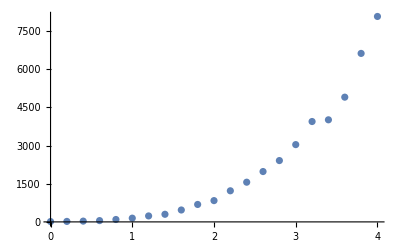

```mathematica
p1 = ListPlot[dat1]
```

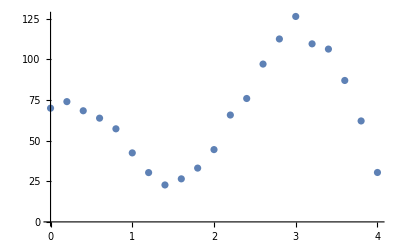

```mathematica
p3 = ListPlot[dat2]
```

### в) С помощью функции Fit найдите наилучшую кривую, аппроксимирующую численные данные

Аппроксимация - приближенное представление сложной функции более простой функцией, имеющей минимальное отклонение от исходной функции. Она не проходит через все узлы, а лежит максимально близко к ним. Использование Fit позволяет найти формулу, которая наилучшим образом соответствует заданному набору данных.

```mathematica
y1 = Fit[dat1, {1, x, x^2, x^3, x^4}, x]
```

97.0905-671.303 x+997.486 x^2-362.244 x^3+69.2603 x^4

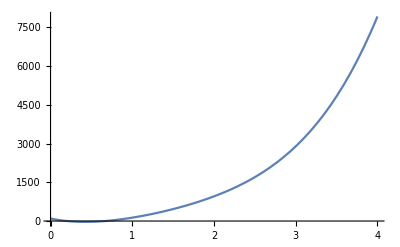

```mathematica
p2 = Plot[y1, {x, 0, 4}]
```

```mathematica
y3 = Fit[dat2, {1, x, Sin[x], Cos[2x]}, x]
```

12.6085+15.5941 x+55.0691 Cos[2 x]+41.7211 Sin[x]

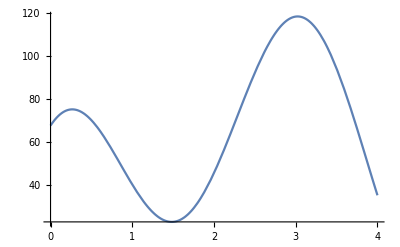

```mathematica
p4 = Plot[y3, {x, 0, 4}]
```

### г) На одной координатной плоскости изобразите найденную кривую вместе с экспериментальными точками

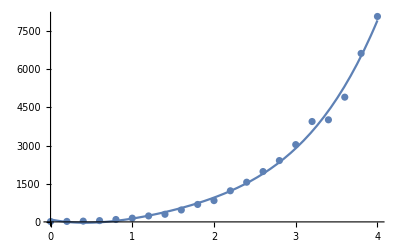

```mathematica
Show[p1,p2]
```

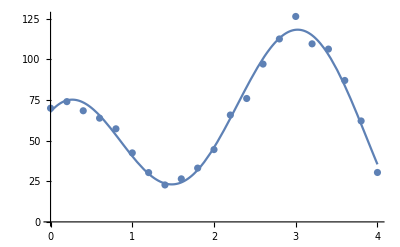

```mathematica
Show[p3, p4]
```